## 1.

```mathematica
ut[v_,w_]:=u[x,y] + pdx (v - x) + pdy (w - y) + pdxx (v - x)^2/(2!)+pdxy (v-x)(w-y) + pdyy (v -y)^2/(2!)+pdxxx (v-x)^3/(3!)+pdxxy ((v-x)^2(w-y))/(2!)+pdxyy ((v-x)(w-y)^2)/(2!)+pdyyy (w-y)^3/(3!)+pdxxxx (v-x)^4/(4!)+pdxxxy ((v-x)^3(w-y))/(3!)+pdxxyy ((v-x)^2(w-y)^2)/(2!*2!)+pdxyyy ((v-x)(w-y)^3)/(3!)+pdyyyy (w-y)^4/(4!);
```

```mathematica
ut[x+h,y+h]-ut[x-h,y+h]-ut[x+h,y-h] +ut[x-h,y-h]
```

## 2.

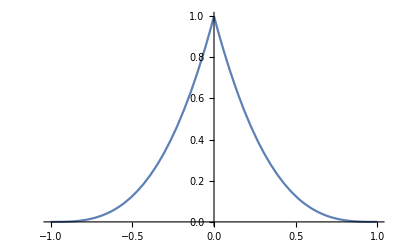

```mathematica
s[x_]:=Piecewise[{{(x + 1)^3, -1≤x≤0}, {(1-x)^3, 0≤x≤1}}]
Plot[s[x],{x,-1,1}]
```

## 5.

```mathematica
∫ⅇ^-x xⅆx
```

ⅇ^-x (-1-x)

```mathematica
∫_0^∞ ⅇ^-x xⅆx
```

1

```mathematica
∫ⅇ^-x x^2 ⅆx
```

ⅇ^-x (-2-2 x-x^2)

```mathematica
∫_0^∞ ⅇ^-x x^2 ⅆx
```

2

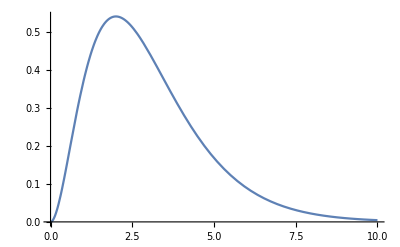

```mathematica
Plot[ⅇ^-x x^2,{x,0,10}]
```

```mathematica
p[x_]:=f[0] + (f[2]-f[0])/2 x + (((f[2]-f[0])/2-f'[2])/2)x(x-2)
```

```mathematica
∫_0^∞ ⅇ^-x p[x]ⅆx
```

1/2 (f[0]+f[2])